```mathematica
dim=8;
Clear[μ,η, A]
(* Parameters to eliminate the magnetic field *)
η=1;
A[1]=1;
A[2]=1;
A[5]=1;
A[6]=B[6]=μ;
A[7]=B[7]=η; (*A[3]=κ; A[4]=λ*)
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/4)*A[4]^(-(x0*x2+x2*x4)/4)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]/2]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/4)*B[4]^(-(x0*x4)/4)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0≤1,x0+=2,For[x2=-1,x2≤1,x2+=2,For[x4=-1,x4≤1,x4+=2,leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];]]]
(*Equates the unrenormalized with the renormalized variables*)

req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4]==leq[4];
req[5]==leq[5];
req[6]==leq[6];
req[7]==leq[7];
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0][[1]];
SB[0]={B[0]->2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0&&B[2]>0&&B[4]>0&&B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0&&B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>=0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0&&B[5]>0&&B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}]
```

{B[0]→2 (A[0]+Log[(μ √(A[3]/(μ+A[3]+μ^2 A[3]+μ A[3]^2)))/(1+μ)]),B[1]→1,B[2]→1,B[3]→((1+μ)^2 A[3] A[4])/(1+μ A[3])^2,B[4]→(μ+A[3])^2/(1+μ A[3])^2,B[5]→1}

Recursive Equation Flow

```mathematica
SIC={B[0]->1,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
Sκλ={A[0]->C,A[1]->1,A[2]->1,A[3]->κ,A[4]->λ,A[5]->1}; (*Just for comparison; not being used in RG flow*)
Sκλ2={κ->A[3],λ->A[4],μ->μ}; (*Just for comparison; not being used in RG flow*)
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
kap[μ_,κ_,λ_]:=(κ λ (1+μ)^2)/(1+κ μ)^2
lam[μ_,κ_,λ_]:=(κ+μ)^2/(1+κ μ)^2
Factor[SBT/.Sκλ]
```

{B[0]→2 (C+Log[(μ √(κ/(κ+μ+κ^2 μ+κ μ^2)))/(1+μ)]),B[1]→1,B[2]→1,B[3]→(κ λ (1+μ)^2)/(1+κ μ)^2,B[4]→(κ+μ)^2/(1+κ μ)^2,B[5]→1}

```mathematica
kap[a,b,c]
lam[a,b,c]
```

((1+a)^2 b c)/(1+a b)^2

(a+b)^2/(1+a b)^2

Jacobian Setup

```mathematica
Clear[μ,κ,λ]
Jaco = Factor[{{D[kap[μ,κ,λ],κ], D[kap[μ,κ,λ],λ]},{D[lam[μ,κ,λ],κ],D[lam[μ,κ,λ],λ]}}];
Simplify[Jaco/.{κ->1,λ->1}]//MatrixForm
Jc = Factor[Eigenvalues[Jaco]];
Jev1[μ_,κ_,λ_]:=-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2+√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)));
Jev2[μ_,κ_,λ_]:=-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2-√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)));
```

((1-μ)/(1+μ) | 1
(2-2 μ)/(1+μ) | 0)

```mathematica
FullSimplify[Expand[Jev2[μ,1,1]]]
```

(1-μ^2+√(-(-1+μ) (1+μ)^2 (9+7 μ)))/(2 (1+μ)^2)

{{μ→1/2 (-1-√5)},{μ→1/2 (-1+√5)}}

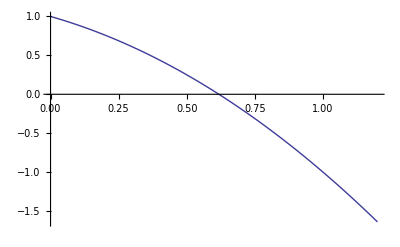

```mathematica
Solve[1-μ-μ^2==0,μ]
Plot[1-μ-μ^2,{μ,0,1.2}]
```

RG flow and convergence check:

* General Parameters

```mathematica
nprec=6000;
μV=N[{1.0,2.0,3.0,4.0,5.0,10,20,100},nprec];
TV=N[2/Log[μV],8];
kmaxV={3000,3000,100000,100000,100000,10000,10000,10000};
ind=0;
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
Clear[λκ,Jocnum,λκ1,Jocnum1,λκ2,Jocnum2,λκ3,Jocnum3,λκ4,Jocnum4,λκ5,Jocnum5,λκ6,Jocnum6,λκ7,Jocnum7]
```

1) μ=1.0; kmax=3000

```mathematica
ind=1; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=lam[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]];
Part[λκ,i][[2]]=kap[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]],
];
]
λκ1=λκ;(* change here *)
```

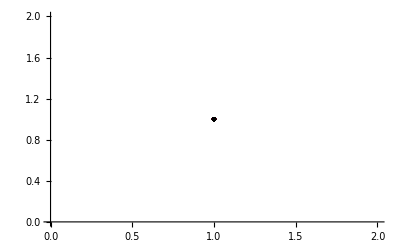

{κ,λ} for the last 50 iterations:(1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.)

```mathematica
λκ=λκ1; (* change here *)
kmax=kmaxV[[1]]; (* change here *)
xyrange={{0.5,1.5},{0,1.5}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black];
Show[Table[Plt[i],{i,1,7}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
```

2) μ=2.0; kmax=3000

```mathematica
ind=2; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=lam[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]];
Part[λκ,i][[2]]=kap[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]],
];
]
λκ2=λκ;(* change here *)
```

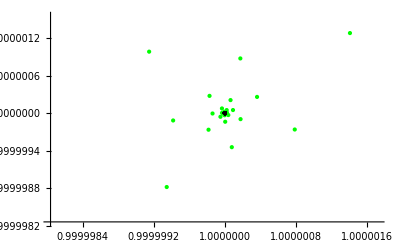

{κ,λ} for the last 50 iterations:(1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.)

```mathematica
λκ=λκ2; (* change here *)
kmax=kmaxV[[2]]; (* change here *)
xyrange={{0.5,1.5},{0,1.5}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black];
Show[Table[Plt[i],{i,1,7}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
```

3) μ=3.0; kmax=100000

```mathematica
ind=3; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=lam[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]];
Part[λκ,i][[2]]=kap[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]],
];
]
λκ3=λκ;
```

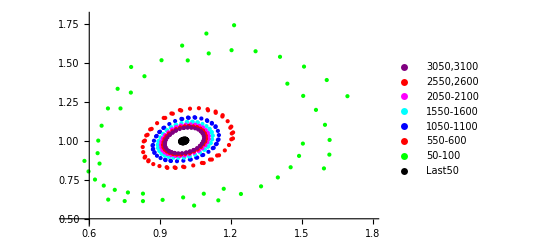

{κ,λ} for the last 50 iterations:(1.00697 | 1.01429
0.985913 | 0.999811
1.00019 | 0.986006
1.01419 | 1.00722
0.992827 | 1.01054
0.989571 | 0.987617)

```mathematica
λκ=λκ3; (* change here *)
kmax=kmaxV[[3]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
(*xyrange=Automatic;*)
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
```

4) μ=4.0; kmax=100000

```mathematica
ind=4; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=lam[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]];
Part[λκ,i][[2]]=kap[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]],
];
]
λκ4=λκ;(* change here*)
```

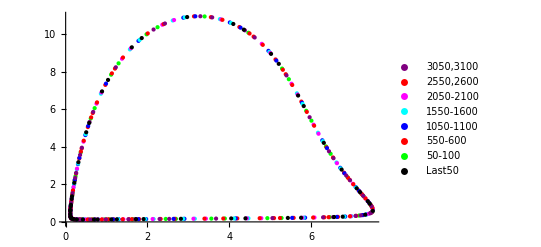

{κ,λ} for the last 50 iterations:(0.575865 | 5.27647
0.176096 | 0.155449
6.56513 | 0.260187
4.35791 | 10.2539
0.115092 | 0.632828
1.72115 | 0.146016)

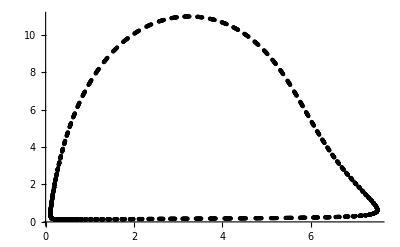

```mathematica
λκ=λκ4; (* change here *)
kmax=kmaxV[[4]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-2000,kmax}],PlotRange->Full,PlotStyle->Black]
```

5) μ=5.0; kmax=100000

```mathematica
ind=5; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=lam[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]];
Part[λκ,i][[2]]=kap[μ,Part[λκ,i-1][[2]],Part[λκ,i-1][[1]]],
];
]
λκ5=λκ;
```

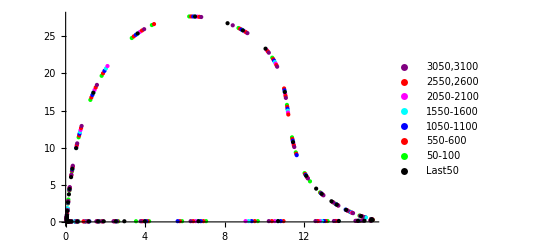

{κ,λ} for the last 50 iterations:(0.0555029 | 0.431944
2.95538 | 0.0864467
12.6125 | 4.4837
0.163997 | 3.71212
0.198373 | 0.0572793
15.4555 | 0.247192)

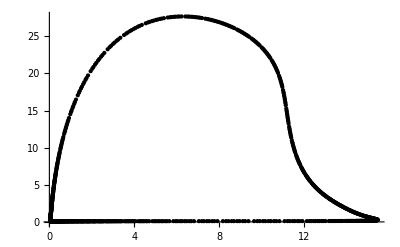

```mathematica
λκ=λκ5; (* change here *)
kmax=kmaxV[[5]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-1000,kmax}],PlotRange->Full,PlotStyle->Black]
```

6) μ=10.0; kmax=10000

```mathematica
ind=6; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=μV[[ind]];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=N[lam[μ,N[Part[λκ,i-1][[2]],nprec],N[Part[λκ,i-1][[1]],nprec]],nprec];
Part[λκ,i][[2]]=N[kap[μ,N[Part[λκ,i-1][[2]],nprec],N[Part[λκ,i-1][[1]],nprec]],nprec],
];
]
λκ6=λκ;
```

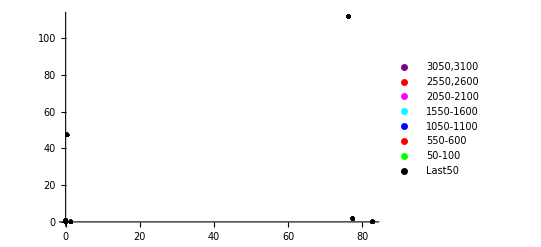

{κ,λ} for the last 50 iterations:(77.38534745 | 1.771768422
0.3955297798 | 47.35292732
0.01460781168 | 0.01006434167
82.71427309 | 0.01468461698
76.25427865 | 111.7424307
0.01184870107 | 0.8242415576)

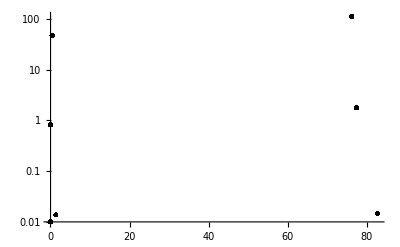

```mathematica
λκ=λκ6; (* change here *)
kmax=kmaxV[[6]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",N[Table[Part[λκ,i],{i,kmax-5,kmax}],10]//MatrixForm];
ListLogPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-2000,kmax}],PlotRange->Full,PlotStyle->Black,PlotStyle->PointSize[Large]]
```

7) μ=20.0; kmax=100000

```mathematica
ind=7; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=μV[[ind]];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=N[lam[μ,N[Part[λκ,i-1][[2]],nprec],N[Part[λκ,i-1][[1]],nprec]],nprec];
Part[λκ,i][[2]]=N[kap[μ,N[Part[λκ,i-1][[2]],nprec],N[Part[λκ,i-1][[1]],nprec]],nprec],
];
]
λκ7=λκ;
```

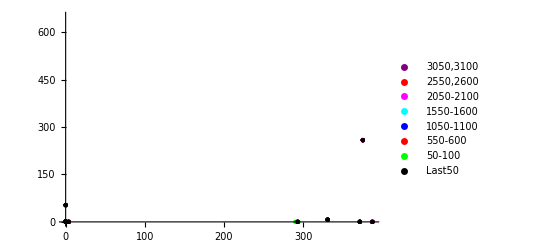

{κ,λ} for the last 50 iterations:(306.8932404 | 703.8642909
0.002643715697 | 0.4806348847
3.724219278 | 0.004975274435
331.0405802 | 6.759212048
0.03860938936 | 53.20619307
0.004723842592 | 0.0007985341252)

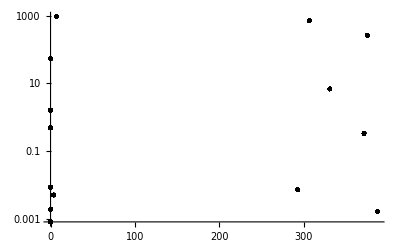

```mathematica
λκ=λκ7; (* change here *)
kmax=kmaxV[[7]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",N[Table[Part[λκ,i],{i,kmax-5,kmax}],10]//MatrixForm];
ListLogPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-2000,kmax}],PlotRange->Full,PlotStyle->Black,PlotStyle->PointSize[Large]]
```

8) μ=100.0; kmax=100000

```mathematica
ind=8; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=μV[[ind]];
λκ=ConstantArray[0,{kmax,2}];
Part[λκ,1][[1]]=lam[μ,μ,1];
Part[λκ,1][[2]]=kap[μ,μ,1];
For[i=1,i<=kmax,i+=1,
If[i>1,
Part[λκ,i][[1]]=N[lam[μ,N[Part[λκ,i-1][[2]],nprec],N[Part[λκ,i-1][[1]],nprec]],nprec];
Part[λκ,i][[2]]=N[kap[μ,N[Part[λκ,i-1][[2]],nprec],N[Part[λκ,i-1][[1]],nprec]],nprec],
];
]
λκ8=λκ;
```

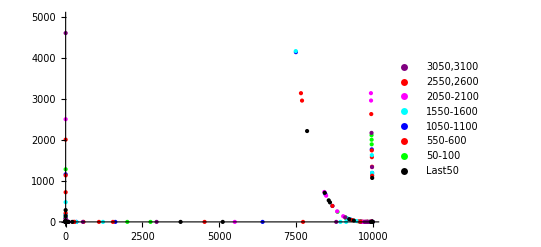

{κ,λ} for the last 50 iterations:(9185.605108 | 40589.61232
0.0001004932944 | 0.2308529354
17.31804902 | 0.00040795414
9231.511255 | 66.53073436
0.0006263450006 | 141.5020361
0.0002912425559 | 4.514735297×10^-6)

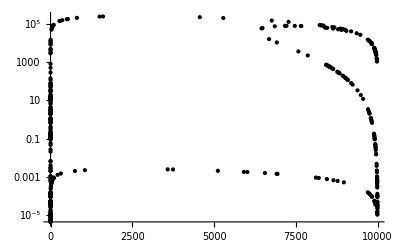

```mathematica
λκ=λκ8; (* change here *)
kmax=kmaxV[[8]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",N[Table[Part[λκ,i],{i,kmax-5,kmax}],10]//MatrixForm];
ListLogPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-400,kmax}],PlotRange->Full,PlotStyle->Black,PlotStyle->PointSize[Large]]
```

************* Same System Size, Fluctuations at temperatures***************

```mathematica
nprec=6000;
Tmax1=10;
Tmin=0.01;
Tinc1=0.02;
Tmax2=30;
Tinc2=0.1;
TV=Join[Range[Tmin,Tmax1, Tinc1], Range[Tmax1+Tinc2,Tmax2, Tinc2]];
μV=N[Exp[2/TV],8];;
kmaxV={100, 200,500};
ind=0;
```

1) System size 100:

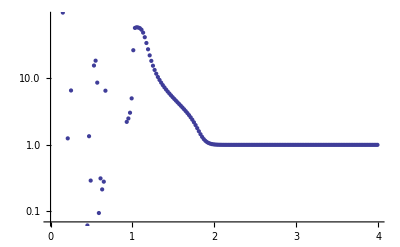

```mathematica
ind=1; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
tκ=ConstantArray[0,{Dimensions[μV][[1]],2}];
For[μi=1,μi<=Dimensions[μV][[1]],μi+=1,
μ=N[μV[[μi]],nprec];
l0=lam[μ,μ,1];
k0=kap[μ,μ,1];
For[i=1,i<kmax,i+=1,
l1=N[lam[μ,k0,l0],nprec];
k1=N[kap[μ,k0,l0],nprec];
k0=k1;
l0=l1;
];
Part[tκ,μi][[1]]=TV[[μi]];
Part[tκ,μi][[2]]=k1
]
tκ1=tκ;
ListLogPlot[Table[{Part[tκ,i][[1]],Part[tκ,i][[2]]},{i,1,200}]]
```

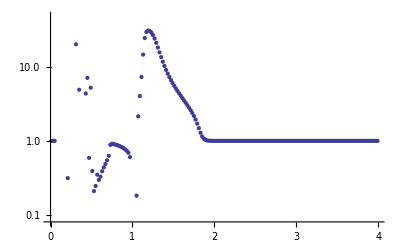

```mathematica
ind=2; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
tκ=ConstantArray[0,{Dimensions[μV][[1]],2}];
For[μi=1,μi<=Dimensions[μV][[1]],μi+=1,
μ=N[μV[[μi]],nprec];
l0=lam[μ,μ^2,1];
k0=kap[μ,μ^2,1];
For[i=1,i<kmax,i+=1,
l1=N[lam[μ,k0,l0],nprec];
k1=N[kap[μ,k0,l0],nprec];
k0=k1;
l0=l1;
];
Part[tκ,μi][[1]]=TV[[μi]];
Part[tκ,μi][[2]]=k1
]
tκ2=tκ;
ListLogPlot[Table[{Part[tκ,i][[1]],Part[tκ,i][[2]]},{i,1,200}]]
```

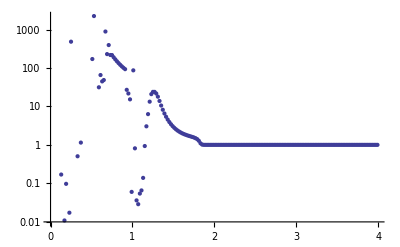

```mathematica
ind=3; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
tκ=ConstantArray[0,{Dimensions[μV][[1]],2}];
For[μi=1,μi<=Dimensions[μV][[1]],μi+=1,
μ=N[μV[[μi]],nprec];
l0=lam[μ,μ,1];
k0=kap[μ,μ,1];
For[i=1,i<kmax,i+=1,
l1=N[lam[μ,k0,l0],nprec];
k1=N[kap[μ,k0,l0],nprec];
k0=k1;
l0=l1;
];
Part[tκ,μi][[1]]=TV[[μi]];
Part[tκ,μi][[2]]=k1
]
tκ3=tκ;
ListLogPlot[Table[{Part[tκ,i][[1]],Part[tκ,i][[2]]},{i,1,200}]]
```

Jocobian Analysis

```mathematica
Clear[κ,λ,μ]
kap[μ_,κ_,λ_]:=(κ λ (1+μ)^2)/(1+κ μ)^2
lam[μ_,κ_,λ_]:=(κ+μ)^2/(1+κ μ)^2
κsols=Factor[Solve[(κ λ (1+μ)^2)/(1+κ μ)^2==κ/.{{λ->(κ+μ)^2/(1+κ μ)^2}},κ]]
Solve[(κ+μ)^2/(1+κ μ)^2==λ,λ];
λsols=Factor[Table[{λ->(κ+μ)^2/(1+κ μ)^2}/.κsols[[i]],{i,1,5}]]
Jev1[μ_,κ_,λ_]:=-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2+√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)));
Jev2[μ_,κ_,λ_]:=-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2-√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)));
```

{{κ→0},{κ→1},{κ→-(-1+μ+μ^2)/μ^2},{κ→-(1+3 μ+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))/(2 μ^2)},{κ→(-1-3 μ+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))/(2 μ^2)}}

{{λ→μ^2},{λ→1},{λ→(-1+μ)^2/μ^2},{λ→((1+3 μ-2 μ^3+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))^2)/(μ^2 (1+μ+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))^2)},{λ→((-1-3 μ+2 μ^3+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))^2)/(μ^2 (-1-μ+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))^2)}}

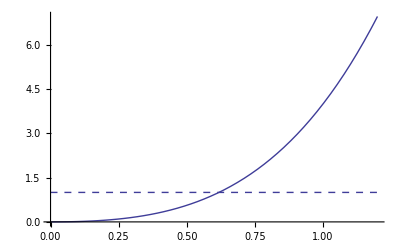

```mathematica
p1=Plot[Jev2[μ,0,μ^2],{μ,0,1.2}];
p2=Plot[1,{μ,0,1.2},PlotStyle->{Dashed}];
Show[p1, p2]
```

1.00125

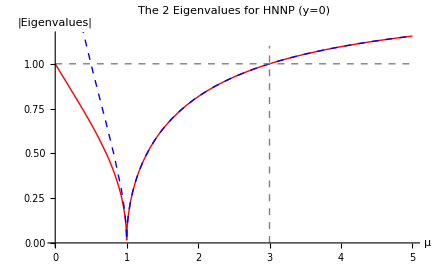

```mathematica
α1=Plot[Abs[Jev1[μ,1,1]],{μ,0,5},PlotStyle->{Red, Thick},AxesLabel->{Style["μ",FontSize->18],Style["|Eigenvalues|",FontSize->14]}];
α2=Plot[Abs[Jev2[μ,1,1]],{μ,0,5},PlotStyle->{Blue, Thick,Dashed},PlotLabel->Style["κ=1,λ=1", FontSize->14],AxesLabel->{"μ","Eigenvalues"}];
lineone=Plot[1,{μ,0,5},PlotStyle->{Dashed,Gray},AxesLabel->{"μ","Eigenvalues"}];
line3=ListPlot[Table[{3,0.01*i},{i,0,110}],Joined->True,PlotStyle->{Dashed,Gray}];
Abs[Jev1[3.01,1,1]]
Show[α1,α2,lineone,line3, PlotLabel->Style["The 2 Eigenvalues for HNNP (y=0)", FontSize->14]]
```

0

μ^2 (1+μ)^2

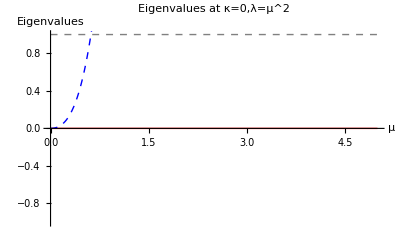

```mathematica
Clear[κ,λ]
α3=Plot[Abs[Jev1[μ,κ,λ]/.{κ->0,λ->μ^2}],{μ,0,5},PlotStyle->{Red, Thick},AxesLabel->{"μ","Eigenvalues"}];
α4=Plot[Abs[Jev2[μ,κ,λ]/.{κ->0,λ->μ^2}],{μ,0,5},PlotStyle->{Blue, Thick,Dashed},PlotLabel->Style["κ=1,λ=1", FontSize->14],AxesLabel->{"μ","Eigenvalues"}];
lineone=Plot[1,{μ,0,5},PlotStyle->{Dashed,Gray},AxesLabel->{"μ","Eigenvalues"}];
Simplify[Jev1[μ,κ,λ]/.{κ->0,λ->μ^2},Assumptions->μ>0]
Simplify[Jev2[μ,κ,λ]/.{κ->0,λ->μ^2},Assumptions->μ>0]
Show[α3,α4,lineone, PlotLabel->Style["Eigenvalues at κ=0,λ=μ^2", FontSize->14]]
```

{{μ→-1},{μ→-1},{μ→1/2 (1-√2)},{μ→1/2 (1+√2)}}

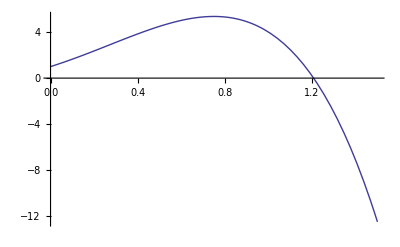

```mathematica
Clear[μ]
Solve[-(1+μ)^2 (-1-4 μ+4 μ^2)==0,μ]
Plot[-(1+μ)^2 (-1-4 μ+4 μ^2),{μ,0,1.5}]
```

```mathematica
JSB=Factor[Table[Jev1[μ,κ,λ]/.{κsols[[i]][[1]],λsols[[i]][[1]][[1]]},{i,1,5}]];
```

```mathematica
JSB/.{μ->0.9}
```

{0.,-0.299193,4.23684-7.02227 ⅈ,-0.126131,-7.02985}

```mathematica
(κsols/.{μ-> 1.02})
```

{{κ→0},{κ→1},{κ→-1.01922},{κ→-2.8815},{κ→-1.02084}}

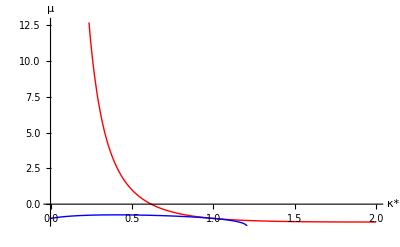

```mathematica
κfp1=Plot[-(-1+μ+μ^2)/μ^2,{μ,0,2},AxesOrigin->{0,0},AxesLabel->{"κ*","μ"},PlotStyle->{Red}];
κfp2=Plot[-(1+3 μ+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))/(2 μ^2),{μ,0,1.5},AxesOrigin->{0,0},AxesLabel->{"κ*","μ"},PlotStyle->{Green}];
κfp3=Plot[(-1-3 μ+√(-(1+μ)^2 (-1-4 μ+4 μ^2)))/(2 μ^2),{μ,0,1.5},AxesOrigin->{0,0},AxesLabel->{"κ*","μ"},PlotStyle->{Blue}];
Show[κfp1,κfp2,κfp3]
```

```mathematica
Plot[-(1+μ)^2 (-1-4 μ+4 μ^2),{μ,0,1.5}]
```

-Graphics-

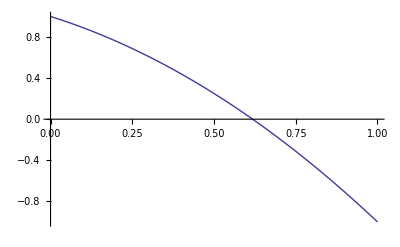

0.618034

```mathematica
Plot[1-μ-μ^2,{μ,0,1}]
1/((1+Sqrt[5.0])/2)
```

```mathematica
1/N[1/2 (1+√2)]
```

0.828427

Sove to find the chaotic transition temperature

a. For the 1st fixed point, κ=λ=1

```mathematica
Simplify[Jev1[μ,1,1],Assumptions->{μ≥1}]
Simplify[Jev2[μ,1,1],Assumptions->{μ≥1}]
Jev1abs[μ_]:=1/2/(1+μ)*Sqrt[(μ-1)^2+(7*μ^2+2*μ-9)]
Simplify[Jev1abs[μ],Assumptions->{μ≥1}]==1
```

-(-1+μ+√(9-2 μ-7 μ^2))/(2 (1+μ))

(1-μ+√(9-2 μ-7 μ^2))/(2+2 μ)

(√2 √(-1+μ^2))/(1+μ)==1

b. For the 2nd fixed point, κ=0, λ=μ^2

```mathematica
Simplify[Jev1[μ,κ,λ]/.{κ->0,λ->μ^2}, Assumptions->{μ>=1}]
Simplify[Jev2[μ,κ,λ]/.{κ->0,λ->μ^2}, Assumptions->{μ>=1}]
```

0

μ^2 (1+μ)^2

```mathematica
Simplify[Jev1abs[μ],Assumptions->{μ≥1}]==1
```

(√2 √(-1+μ^2))/(1+μ)==1

```mathematica
FullSimplify[Jev1[μ,κ,λ]]
FullSimplify[Jev2[μ,κ,λ]]
```

-((1+μ) (-λ+(-1+κ) λ μ+κ λ μ^2+√(λ^2 (1+μ)^2 (-1+κ μ)^2-8 κ (κ+μ) (1+κ μ) (-1+μ^2))))/(2 (1+κ μ)^3)

-((1+μ) (-λ+(-1+κ) λ μ+κ λ μ^2-√(λ^2 (1+μ)^2 (-1+κ μ)^2-8 κ (κ+μ) (1+κ μ) (-1+μ^2))))/(2 (1+κ μ)^3)

```mathematica
-((1+μ) (-λ+(-1+κ+κμ) λ μ+√(λ^2 (1+μ)^2 (-1+κ μ)^2-8 κ (κ+μ) (1+κ μ) (-1+μ^2))))/(2 (1+κ μ)^3)
```